```mathematica
SetDirectory["D:\\saveAndLoad\\organisms"]
```

D:\saveAndLoad\organisms

```mathematica
SetDirectory["D:\\grafiliv - stayin alive\\organisms"]
```

D:\grafiliv - stayin alive\organisms

```mathematica
GetOrganism[orgNo_]:=With[{path=StringForm["org``.json",orgNo]//ToString},
Import[path]
]
```

```mathematica
GenomeSize[orgNo_]:=With[{
g ="genome"/.GetOrganism[orgNo]
},
Length["vertices"/.g]+Length["links"/.g]
]
```

```mathematica
oMax=Length[FileNames[]]-1;
δo=Ceiling[oMax/500];
frames=Table[frame,{frame,0,oMax,δo}];
data=ParallelMap[GenomeSize,frames];
```

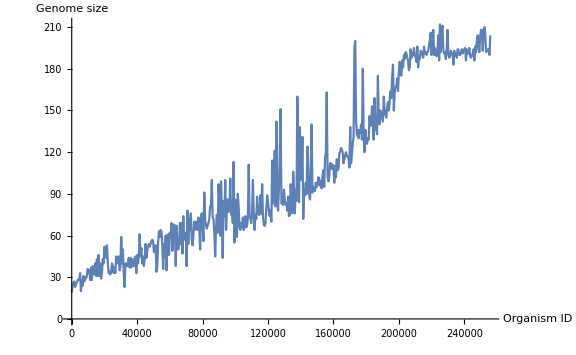

```mathematica
ListLinePlot[data,DataRange->{0,oMax},AxesLabel->{"Organism ID","Genome size"}, ImageSize->Large]
```